```mathematica
Clear[x,y]
f[x_,y_]=4*x + 1.3 * y^2;
a=0;b=1;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];
x0=0;y0=0.4;
eulk1=Table[{x0,y0}={x0+h1,y0+h1/2*(f[x0,y0]+f[x0+h1,y0+h1*f[x0,y0]])},{i,0,n1-1}]
```

{{0.1,0.44191},{0.2,0.531331},{0.3,0.676978},{0.4,0.894457},{0.5,1.21369},{0.6,1.69692},{0.7,2.49132},{0.8,4.02697},{0.9,8.12951},{1.,31.7698}}

```mathematica
eulk1=Prepend[eulk1,{0,0}]
```

{{0,0},{0.1,0.44191},{0.2,0.531331},{0.3,0.676978},{0.4,0.894457},{0.5,1.21369},{0.6,1.69692},{0.7,2.49132},{0.8,4.02697},{0.9,8.12951},{1.,31.7698}}

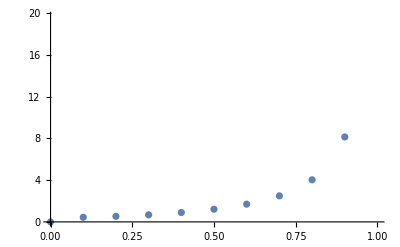

```mathematica
gr1=ListPlot[eulk1]
```

```mathematica
Clear[x,y]
f[x_,y_]=4*x + 1.3 * y^2;
a=0;b=1;h1=0.1;h2=0.05;n2=Floor[(b-a)/h2];
x0=0;y0=0.4;
eulk2=Table[{x0,y0}={x0+h2,y0+h2/2*(f[x0,y0]+f[x0+h2,y0+h2*f[x0,y0]])},{i,0,n2-1}]
```

{{0.05,0.415674},{0.1,0.442493},{0.15,0.481196},{0.2,0.532722},{0.25,0.598304},{0.3,0.679595},{0.35,0.778855},{0.4,0.899214},{0.45,1.04509},{0.5,1.22286},{0.55,1.442},{0.6,1.7171},{0.65,2.07168},{0.7,2.54616},{0.75,3.21571},{0.8,4.23667},{0.85,5.99094},{0.9,9.67715},{0.95,21.1678},{1.,118.751}}

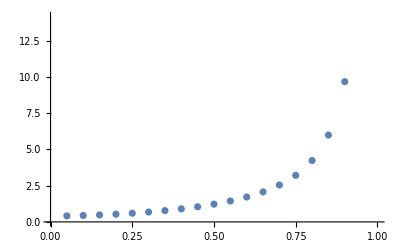

```mathematica
gr2=ListPlot[eulk2]
```

```mathematica
(*б)Метод Рунге-Кутта*)
```

```mathematica
Clear[x,y]
f[x_,y_]=4*x + 1.3 * y^2;
a=0;b=1;x0=0;y0=0.4;h1=0.1;h2=0.05;n1=Floor[(b-a)/h1];n2=Floor[(b-a)/h2];
sol1=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n1+1,k++,
k1[x_,y_]=h1*f[x,y];
k2[x_,y_]=h1*f[x+h1/2,y+k1[x,y]/2];
k3[x_,y_]=h1*f[x+h1/2,y+k2[x,y]/2];
k4[x_,y_]=h1*f[x+h1,y+k3[x,y]];
x=x+h1;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol1=Append[sol1,{x,y}]]
sol1
```

{{0,0.4},{0.1,0.442697},{0.2,0.5332},{0.3,0.680488},{0.4,0.90084},{0.5,1.22605},{0.6,1.72438},{0.7,2.56748},{0.8,4.33136},{0.9,10.7211},{1.,571.622}}

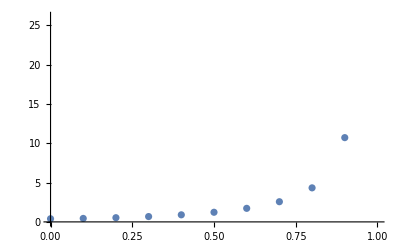

```mathematica
gr3=ListPlot[sol1]
```

```mathematica
Clear[so12]
sol2=List[{x0,y0}];
x=x0;y=y0;
For[k=1,k<n2+1,k++,
k1[x_,y_]=h2*f[x,y];
k2[x_,y_]=h2*f[x+h2/2,y+k1[x,y]/2];
k3[x_,y_]=h2*f[x+h2/2,y+k2[x,y]/2];
k4[x_,y_]=h2*f[x+h2,y+k3[x,y]];
x=x+h2;
y=y+(k1[x,y]+2*k2[x,y]+2*k3[x,y]+k4[x,y])/6;
sol2=Append[sol2,{x,y}]]
sol2
```

{{0,0.4},{0.05,0.415768},{0.1,0.442694},{0.15,0.481521},{0.2,0.533193},{0.25,0.598955},{0.3,0.680475},{0.35,0.780038},{0.4,0.900818},{0.45,1.04731},{0.5,1.22601},{0.55,1.44665},{0.6,1.72432},{0.65,2.08362},{0.7,2.56751},{0.75,3.25807},{0.8,4.33398},{0.85,6.27113},{0.9,10.8914},{0.95,35.6741},{1.,130109.}}

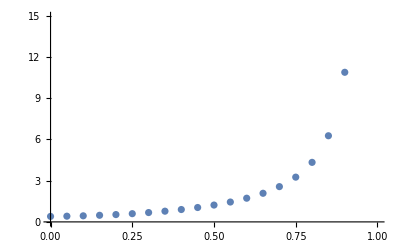

```mathematica
gr4=ListPlot[sol2]
```

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
sol2 = DSolve[{y'[x] == f[x,y[x]], y[x0]== y0},  y[x],x];
y1[x_] = y[x]/.Flatten[sol2]
```

-((0.877058 (1. x^(3/2) BesselJ[-4/3,1.52023 x^(3/2)]-0.823439 x^(3/2) BesselJ[-2/3,1.52023 x^(3/2)]+0.438529 BesselJ[-1/3,1.52023 x^(3/2)]-1. x^(3/2) BesselJ[2/3,1.52023 x^(3/2)]))/(x (1. BesselJ[-1/3,1.52023 x^(3/2)]-0.411719 BesselJ[1/3,1.52023 x^(3/2)])))

```mathematica
Clear[y,x]  (*Очистка предыдущих определений*)
sol3 = NDSolve[{y'[x] == f[x,y[x]], y[x0]== y0},  y[x],{x,0 ,1}];
y2[x_] = y[x]/.Flatten[sol2]
```

InterpolatingFunction[…][x]

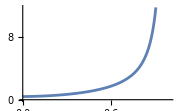

```mathematica
gr5=Plot[y1[x], {x,0,1}, ImageSize-> Small]
```

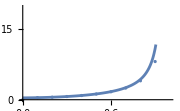

```mathematica
Show[gr1,gr5,ImageSize->Small]
```

```mathematica
gr6=Plot[y2[x], {x,0,1}, ImageSize-> Small]
```

-Graphics-

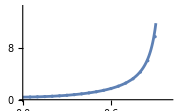

```mathematica
Show[gr2,gr6,ImageSize->Small]
```

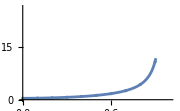

```mathematica
Show[gr3,gr5,ImageSize->Small]
```

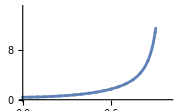

```mathematica
Show[gr4,gr5,ImageSize->Small]
```